## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext -> Notebook]
removeInputFiles =  True;
removeOutputFiles = True;

rxnName="G6PDH2r";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName= "kinetic_data_trp3_milos_assume_Km_desktop_adjusted_KEQS.csv";

mainFolder = "fit_G6PDH2r_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

(g6p^c+nadp^c⇌(6pgl)^c+nadph^c)^G6PDH2r

random sequential (nad); ordered sequential (nadp)

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp | Null
g6p | Null | 15.6637 | 14.8805
16.4469 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.000145 | 0.00013775
0.00015225 | nadp | 0.00018 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02
1 | nadp | 0.000015 | 0.00001425
0.00001575 | g6p | 0.001 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02
1 | nad | 0.00167 | 0.0015865
0.0017535 | g6p | 0.001 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp | Null
g6p | Null | 155. | 147.25
162.75 | 1/s | 7.5 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g6p^c+nadp^c⇌(6pgl)^c+nadph^c)^G6PDH2r

random sequential (nad); ordered sequential (nadp)

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp | Null
g6p | Null | 15.6637 | 14.8805
16.4469 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.000145 | 0.00013775
0.00015225 | nadp | 0.00018 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02
1 | nadp | 0.000015 | 0.00001425
0.00001575 | g6p | 0.001 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp | Null
g6p | Null | 155. | 147.25
162.75 | 1/s | 7.5 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_G6PDH2r[c] + nadp[c] <=> E_G6PDH2r[c]&nadp",
				"E_G6PDH2r[c]&nadp + g6p[c] <=> E_G6PDH2r[c]&nadp&g6p",
				"E_G6PDH2r[c]&nadp&g6p <=> E_G6PDH2r[c]&6pgl&nadph",
				"E_G6PDH2r[c]&6pgl&nadph <=> E_G6PDH2r[c]&6pgl + nadph[c]",
				"E_G6PDH2r[c]&6pgl <=> E_G6PDH2r[c] + 6pgl[c]"};



enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((G6PDH2r^c)_^+nadp^c⇌(G6PDH2r^c&nadp^c)_^)^G6PDH2r1,((G6PDH2r^c&(6pgl)^c)_^⇌(G6PDH2r^c)_^+(6pgl)^c)^G6PDH2r2,((G6PDH2r^c&nadp^c)_^+g6p^c⇌(G6PDH2r^c&nadp^c&g6p^c)_^)^G6PDH2r3,((G6PDH2r^c&(6pgl)^c&nadph^c)_^⇌(G6PDH2r^c&(6pgl)^c)_^+nadph^c)^G6PDH2r4,((G6PDH2r^c&nadp^c&g6p^c)_^⇌(G6PDH2r^c&(6pgl)^c&nadph^c)_^)^G6PDH2r5}

```mathematica
Print[enzymeModel]
```

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G6PDH2r^c)_^+nadp^c⇌(G6PDH2r^c&nadp^c)_^)^G6PDH2r1,Overscript[(G6PDH2r^c&(6pgl)^c)_^⇌(G6PDH2r^c)_^+(6pgl)^c, G6PDH2r2],((G6PDH2r^c&nadp^c)_^+g6p^c⇌(G6PDH2r^c&nadp^c&g6p^c)_^)^G6PDH2r3,Overscript[(G6PDH2r^c&(6pgl)^c&nadph^c)_^⇌(G6PDH2r^c&(6pgl)^c)_^+nadph^c, G6PDH2r4],((G6PDH2r^c&nadp^c&g6p^c)_^⇌(G6PDH2r^c&(6pgl)^c&nadph^c)_^)^G6PDH2r5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((G6PDH2r^c&nadp^c&g6p^c)_^-((G6PDH2r^c&(6pgl)^c&nadph^c)_^)/K_G6PDH2r5) Volume_c k_G6PDH2r5^⟶}

Volume_c (-(G6PDH2r^c&(6pgl)^c&nadph^c)_^ k_G6PDH2r5^⟵+(G6PDH2r^c&nadp^c&g6p^c)_^ k_G6PDH2r5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Print[enzymeModel]
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
Print[enzymeModel]
```

```mathematica
FilePrint@dataPathList
```

Priority	6pgl[c]	g6p[c]	nadp[c]	nadph[c]	param_G6PDH2r_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0.000014499999999999983	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.09090909090909083
1	0	0.000022980951290686127	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.13680688860320991
1	0	0.0000364223532568889	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.20076000891310172
1	0	0.00005772553973025699	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.284747248950801
1	0	0.00009148881494962787	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.3868631798468566
1	0	0.00014499999999999984	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.4999999999999997
1	0	0.00022980951290686128	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.6131368201531429
1	0	0.000364223532568889	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.7152527510491985
1	0	0.0005772553973025704	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.7992399910868981
1	0	0.0009148881494962787	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.8631931113967897
1	0	0.0014499999999999984	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.909090909090909
1	0	0.001	1.5000000000000005e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.09090909090909093
1	0	0.001	2.377339788691672e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.13680688860321008
1	0	0.001	3.767829647264374e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.20076000891310192
1	0	0.001	5.971607558302455e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.2847472489508013
1	0	0.001	9.464360167202897e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.3868631798468569
1	0	0.001	0.000015000000000000004	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.5
1	0	0.001	0.000023773397886916717	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.6131368201531432
1	0	0.001	0.000037678296472643745	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.7152527510491988
1	0	0.001	0.000059716075583024555	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.799239991086898
1	0	0.001	0.00009464360167202897	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.86319311139679
1	0	0.001	0.00015000000000000004	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.909090909090909
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.
1	0	1	1	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt"	155.

### Simulate data with uncertainty

```mathematica
nSamples=100;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	20
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_6pgl.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_6pgl.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.526672958125
best_fit: 1.01263351112
best_fit: 1.05782227706
best_fit: 0.922336234122
best_fit: 1.06188925871

```mathematica
Print[paramFitSub]
```

paramFitSub

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | haldaneRatio_1 | 9.40554×10^-11 | 8.84642×10^-21 | 3.39229×10^-9 | 2.1657×10^-8 | 15.6637 | 15.6637
1 | relRateFor_g6p | 0.0000233847 | 5.46846×10^-10 | 4.8949×10^-6 | 0.00538439 | 0.0909091 | 0.0909042
1 | relRateFor_g6p | 0.0000190247 | 3.61939×10^-10 | 5.99283×10^-6 | 0.0043805 | 0.136807 | 0.136801
1 | relRateFor_g6p | 0.0000129494 | 1.67688×10^-10 | 5.98601×10^-6 | 0.00298168 | 0.20076 | 0.200754
1 | relRateFor_g6p | 4.97091×10^-6 | 2.47099×10^-11 | 3.25918×10^-6 | 0.00114459 | 0.284747 | 0.284744
1 | relRateFor_g6p | 4.73×10^-6 | 2.23729×10^-11 | 4.21344×10^-6 | 0.00108913 | 0.386863 | 0.386867
1 | relRateFor_g6p | 0.0000154781 | 2.39573×10^-10 | 0.0000178202 | 0.00356403 | 0.5 | 0.500018
1 | relRateFor_g6p | 0.0000262265 | 6.87831×10^-10 | 0.0000370277 | 0.00603906 | 0.613137 | 0.613174
1 | relRateFor_g6p | 0.0000359281 | 1.29083×10^-9 | 0.0000591736 | 0.0082731 | 0.715253 | 0.715312
1 | relRateFor_g6p | 0.0000439076 | 1.92787×10^-9 | 0.000080808 | 0.0101106 | 0.79924 | 0.799321
1 | relRateFor_g6p | 0.0000499837 | 2.49837×10^-9 | 0.0000993521 | 0.0115098 | 0.863193 | 0.863292
1 | relRateFor_g6p | 0.0000543445 | 2.95332×10^-9 | 0.000113764 | 0.0125141 | 0.909091 | 0.909205
1 | relRateFor_nadp | 2.41809×10^-6 | 5.84715×10^-12 | 5.06167×10^-7 | 0.000556784 | 0.0909091 | 0.0909086
1 | relRateFor_nadp | 1.96711×10^-6 | 3.86951×10^-12 | 6.19656×10^-7 | 0.000452942 | 0.136807 | 0.136806
1 | relRateFor_nadp | 1.33872×10^-6 | 1.79217×10^-12 | 6.18844×10^-7 | 0.000308251 | 0.20076 | 0.200759
1 | relRateFor_nadp | 5.13477×10^-7 | 2.63658×10^-13 | 3.36663×10^-7 | 0.000118232 | 0.284747 | 0.284747
1 | relRateFor_nadp | 4.89896×10^-7 | 2.39998×10^-13 | 4.36392×10^-7 | 0.000112803 | 0.386863 | 0.386864
1 | relRateFor_nadp | 1.60156×10^-6 | 2.565×10^-12 | 1.84387×10^-6 | 0.000368774 | 0.5 | 0.500002
1 | relRateFor_nadp | 2.71323×10^-6 | 7.36161×10^-12 | 3.83055×10^-6 | 0.000624746 | 0.613137 | 0.613141
1 | relRateFor_nadp | 3.71661×10^-6 | 1.38132×10^-11 | 6.12102×10^-6 | 0.000855784 | 0.715253 | 0.715259
1 | relRateFor_nadp | 4.54186×10^-6 | 2.06285×10^-11 | 8.35851×10^-6 | 0.00104581 | 0.79924 | 0.799248
1 | relRateFor_nadp | 5.17026×10^-6 | 2.67316×10^-11 | 0.0000102763 | 0.0011905 | 0.863193 | 0.863203
1 | relRateFor_nadp | 5.62125×10^-6 | 3.15984×10^-11 | 0.0000117668 | 0.00129435 | 0.909091 | 0.909103
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.
1 | absRateFor | 1.66852×10^-9 | 2.78396×10^-18 | 5.95496×10^-7 | 3.84191×10^-7 | 155. | 155.

### Simulated Data and Best Fit Data Plot

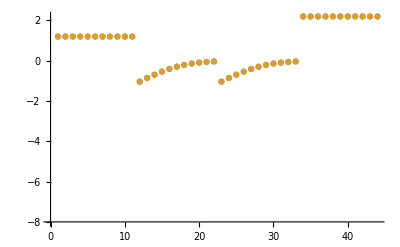

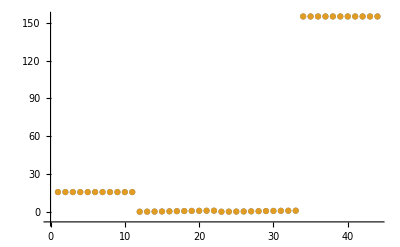

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

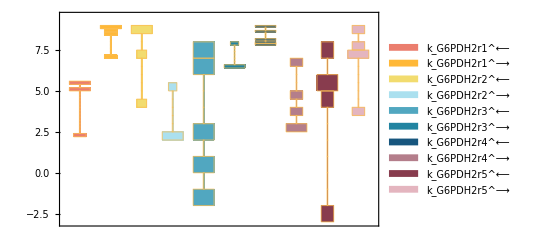

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

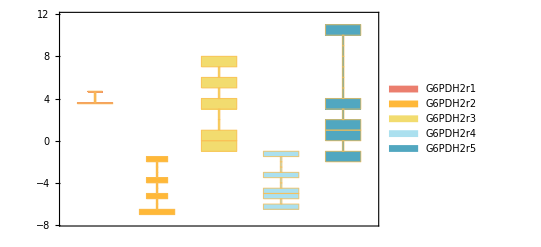

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

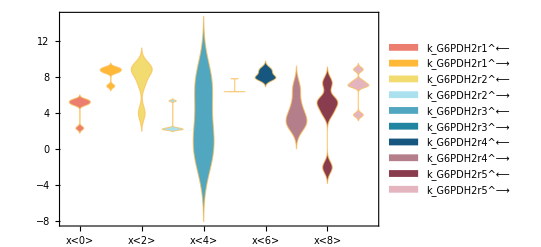

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

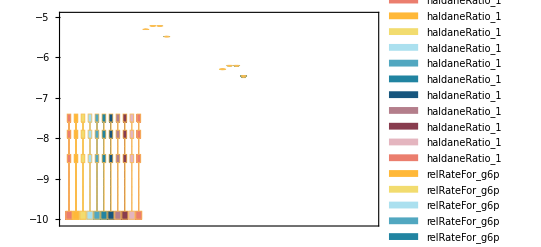

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.000145 | 0.00014499 | 0.00712678
0.000015 | 0.0000149999 | 0.000737533

```mathematica
Print[relativeRateForward]
```

{(g6p^c (k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+nadp^c k_G6PDH2r1^⟶ (k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶)))))/(g6p^c k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+nadp^c k_G6PDH2r1^⟶ (g6p^c k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶)))),(nadp^c (g6p^c k_G6PDH2r1^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+k_G6PDH2r1^⟶ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶))))/(g6p^c k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+nadp^c k_G6PDH2r1^⟶ (g6p^c k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶))))}

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
155. | 155. | 3.84191×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
15.6637 | 15.6637 | 2.1657×10^-8

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
15.6637 | 15.6637 | 2.1657×10^-8

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

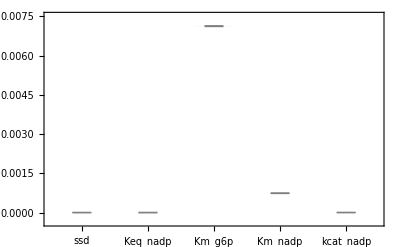

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse];
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r\rateconst_labels_g6pdh2r.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r\S_g6pdh2r.txt

```mathematica
"/Users/guest/Desktop/internship stuff/MASSef/examples/chors\\S_chors.txt"
```

/Users/guest/Desktop/internship stuff/MASSef/examples/chors\S_chors.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_G6PDH2r[c],E_G6PDH2r[c]&6pgl,E_G6PDH2r[c]&nadp,E_G6PDH2r[c]&6pgl&nadph,6pgl[c],g6p[c],nadp[c],nadph[c],E_G6PDH2r[c]&nadp&g6p}

/Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r\species_g6pdh2r.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{G6PDH2r1: E_G6PDH2r[c] + nadp[c] <=> E_G6PDH2r[c]&nadp,G6PDH2r2: E_G6PDH2r[c]&6pgl <=> 6pgl[c] + E_G6PDH2r[c],G6PDH2r3: E_G6PDH2r[c]&nadp + g6p[c] <=> E_G6PDH2r[c]&nadp&g6p,G6PDH2r4: E_G6PDH2r[c]&6pgl&nadph <=> E_G6PDH2r[c]&6pgl + nadph[c],G6PDH2r5: E_G6PDH2r[c]&nadp&g6p <=> E_G6PDH2r[c]&6pgl&nadph}

/Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r\reactions_g6pdh2r.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_G6PDH2r[c],E_G6PDH2r[c]&6pgl,E_G6PDH2r[c]&nadp,E_G6PDH2r[c]&6pgl&nadph,E_G6PDH2r[c]&nadp&g6p}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_G6PDH2r1_rev*k_G6PDH2r2_fwd*k_G6PDH2r3_rev*k_G6PDH2r4_fwd*param_G6PDH2r_total) - k_G6PDH2r1_rev*k_G6PDH2r2_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd*param_G6PDH2r_total - g6p(c)*k_G6PDH2r2_fwd*k_G6PDH2r3_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd*param_G6PDH2r_total - k_G6PDH2r1_rev*k_G6PDH2r2_fwd*k_G6PDH2r3_rev*k_G6PDH2r5_rev*param_G6PDH2r_total - k_G6PDH2r1_rev*k_G6PDH2r3_rev*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadph(c)*param_G6PDH2r_total)/(k_G6PDH2r1_rev*k_G6PDH2r2_fwd*k_G6PDH2r3_rev*k_G6PDH2r4_fwd + 6pgl(c)*k_G6PDH2r1_rev*k_G6PDH2r2_rev*k_G6PDH2r3_rev*k_G6PDH2r4_fwd + k_G6PDH2r1_rev*k_G6PDH2r2_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd + 6pgl(c)*k_G6PDH2r1_rev*k_G6PDH2r2_rev*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd + g6p(c)*k_G6PDH2r2_fwd*k_G6PDH2r3_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd + 6pgl(c)*g6p(c)*k_G6PDH2r2_rev*k_G6PDH2r3_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd + k_G6PDH2r1_rev*k_G6PDH2r2_fwd*k_G6PDH2r3_rev*k_G6PDH2r5_rev + 6pgl(c)*k_G6PDH2r1_rev*k_G6PDH2r2_rev*k_G6PDH2r3_rev*k_G6PDH2r5_rev + g6p(c)*k_G6PDH2r1_fwd*k_G6PDH2r2_fwd*k_G6PDH2r3_fwd*k_G6PDH2r4_fwd*nadp(c) + k_G6PDH2r1_fwd*k_G6PDH2r2_fwd*k_G6PDH2r3_rev*k_G6PDH2r4_fwd*nadp(c) + g6p(c)*k_G6PDH2r1_fwd*k_G6PDH2r2_fwd*k_G6PDH2r3_fwd*k_G6PDH2r5_fwd*nadp(c) + k_G6PDH2r1_fwd*k_G6PDH2r2_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd*nadp(c) + g6p(c)*k_G6PDH2r1_fwd*k_G6PDH2r3_fwd*k_G6PDH2r4_fwd*k_G6PDH2r5_fwd*nadp(c) + g6p(c)*k_G6PDH2r1_fwd*k_G6PDH2r2_fwd*k_G6PDH2r3_fwd*k_G6PDH2r5_rev*nadp(c) + k_G6PDH2r1_fwd*k_G6PDH2r2_fwd*k_G6PDH2r3_rev*k_G6PDH2r5_rev*nadp(c) + 6pgl(c)*k_G6PDH2r1_rev*k_G6PDH2r2_rev*k_G6PDH2r3_rev*k_G6PDH2r4_rev*nadph(c) + 6pgl(c)*k_G6PDH2r1_rev*k_G6PDH2r2_rev*k_G6PDH2r4_rev*k_G6PDH2r5_fwd*nadph(c) + 6pgl(c)*g6p(c)*k_G6PDH2r2_rev*k_G6PDH2r3_fwd*k_G6PDH2r4_rev*k_G6PDH2r5_fwd*nadph(c) + 6pgl(c)*k_G6PDH2r1_rev*k_G6PDH2r2_rev*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadph(c) + 6pgl(c)*g6p(c)*k_G6PDH2r2_rev*k_G6PDH2r3_fwd*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadph(c) + k_G6PDH2r1_rev*k_G6PDH2r3_rev*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadph(c) + 6pgl(c)*k_G6PDH2r2_rev*k_G6PDH2r3_rev*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadph(c) + g6p(c)*k_G6PDH2r1_fwd*k_G6PDH2r3_fwd*k_G6PDH2r4_rev*k_G6PDH2r5_fwd*nadp(c)*nadph(c) + g6p(c)*k_G6PDH2r1_fwd*k_G6PDH2r3_fwd*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadp(c)*nadph(c) + k_G6PDH2r1_fwd*k_G6PDH2r3_rev*k_G6PDH2r4_rev*k_G6PDH2r5_rev*nadp(c)*nadph(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r\rateconst_clusters_g6pdh2r.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/g6pdh2r\rateLaw_g6pdh2r.txt